## Data

```mathematica
(* Initialize stuff *)
```

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Load and extract data *)
```

```mathematica
vrad =SemanticImport["vrad_simu_challenge_0.rdb",ExcludedLines->{2}];
```

```mathematica
data =Normal@vrad[All,#]&/@ {"jdb",(#"rv_planet"+#"rv_osc_and_gran"+#"rv_inst_noise") 1000&,(#"sig_rv"*1000)^2 &};
```

```mathematica
Clear[rvmodel,chi2];
rvmodel[phi_,P_,logK_]:=Module[{f,K=Exp[logK]},
f = 2 Pi (FractionalPart[data[[1]]/P]+phi);
rv = K Cos[f]
]
chi2[phi_?NumericQ,P_?NumericQ,logK_?NumericQ]:=Module[{rv},
rv = rvmodel[phi,P,logK];
Total[(data[[2]]- rv)^2/data[[3]]]
]
```

```mathematica
(* Try a test *)
```

```mathematica
chi2[0.75,16.0,Log[1.5]]
```

2428.85

```mathematica
Clear[plot1,plot2];
plot1[logP_]:=ListPlot[Transpose[{FractionalPart[data[[1]]/Exp[logP]],data[[2]]}]]
plot2[logK_,phi_,st_:Red]:= Plot[Exp[logK]Cos[2 Pi (t + phi)],{t,0,1},PlotStyle->st]
```

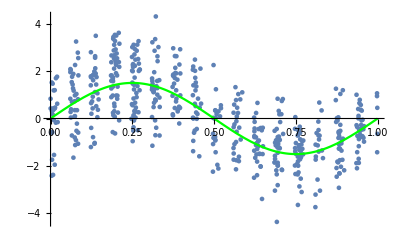

```mathematica
Show[plot1[Log[16]],plot2[Log[1.5],0.75,Green]]
```

## Gaussian Mixtures

We describe our Gaussian mixture as a list of lists, where each entry is {wt, mean, covar}

```mathematica
Clear[buildModels,mkRandom];
buildModels[ll_]:=Module[{wt,models},
wt = ll[[All,1]];
models = MultinormalDistribution@@@ ll[[All,2;;3]];
{wt,models}
];
mkRandom[ll_,n_]:= RandomVariate[MixtureDistribution@@ll, n];
```

## Test case

### The PMC loop

#### Initialize

```mathematica
(* Initialize *)
nd=10;
npop=10000;
mix1 = Table[{0.5/nd,{i/nd,15.55+i/nd,-0.5+i/nd},DiagonalMatrix[{1.0,0.1,0.4}]},{i,0.0,nd-1}];
mix2 = Table[{0.5/nd,{i/nd,24.55+i/nd,-0.5+i/nd},DiagonalMatrix[{1.0,0.1,0.4}]},{i,0.0,nd-1}];
mix = Join[mix1,mix2];
model= buildModels@mix;
eps = DiagonalMatrix[{0.01,0.001,0.01}^2];
reg = 1;
```

#### First look plots

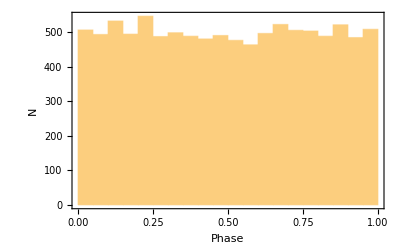

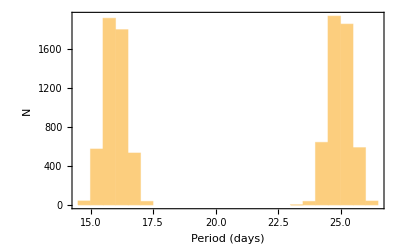

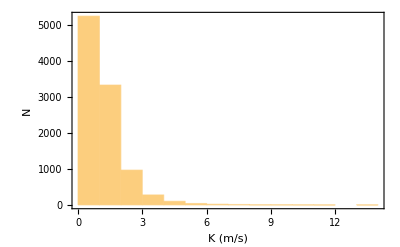

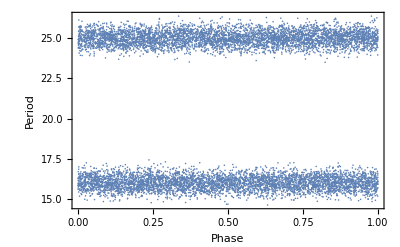

```mathematica
xx = mkRandom[model,npop]; (* One off for simplicity *)
xx ={Mod[#1,1],#2,#3}&@@@ xx;
Histogram[xx[[All,1]],Frame->True,Axes->False,FrameLabel->{"Phase","N"}]
Histogram[xx[[All,2]],Frame->True,Axes->False,FrameLabel->{"Period (days)","N"}]
Histogram[Exp[xx[[All,3]]],Frame->True,Axes->False,FrameLabel->{"K (m/s)","N"}]
ListPlot[xx[[All,{1,2}]],Frame->True,Axes->False,FrameLabel->{"Phase","Period"}]
```

#### The PMC Loop

```mathematica
(* The PMC loop starts here, execute this cell until the perplexity
gets close to 1 *)
(* Generate npop randoms and calculate the posterior at these points*)
perplex=0;
While[perplex < 0.95,
xx = mkRandom[model,npop];
xx ={Mod[#1,1],#2,#3}&@@@ xx;
lik = chi2@@@ xx;
lik = lik - Min[lik];
lik = Exp[-lik/2];
(* Now compute the PDF for each of the mixtures and weight*)
pps = PDF[#,xx]&/@ model[[2]];
pps = pps*model[[1]]; 
totpp = Total[pps,1];
pps = #/totpp & /@ pps;
(* Compute weights *)
wt = lik/totpp;
wt = wt/Total[wt];
(* Perplexity *)
perplex=Exp[-Total[wt Log[wt]]]/npop;
(* Now do the update step *)
mix = Module[{a, mu, sig,dx,dx1},
a = Total[wt* #];
mu = Total[wt*#*xx,1]/a;
dx = #-mu & /@ xx;
dx1 = dx*wt*#;
sig = (Transpose[dx1].dx)/a + reg*eps;
{a,mu,sig}]&/@ pps;
dets = Det[#]&/@ mix[[All,3]];
If[(Length@Select[dets,#≤0 &]) >0,Print["Determinant Problem"];Break[]];
reg = reg/1.2;
model=buildModels[mix];
]
perplex
Mean[MixtureDistribution@@model]
StandardDeviation[MixtureDistribution@@model]
```

0.950611

{0.746481,15.9991,0.408459}

{0.00729044,0.0018794,0.0196992}

### Summary plots

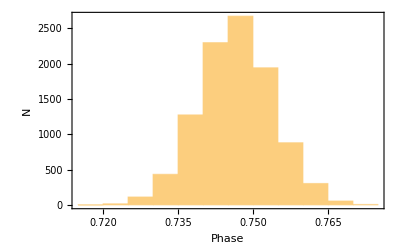

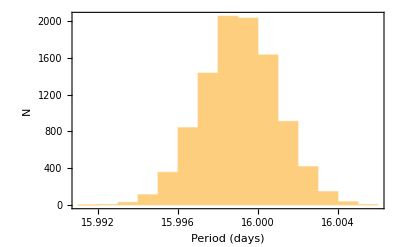

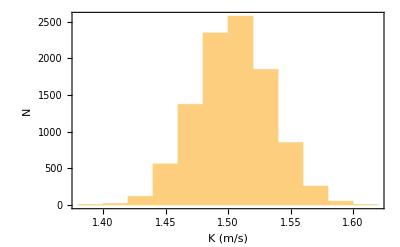

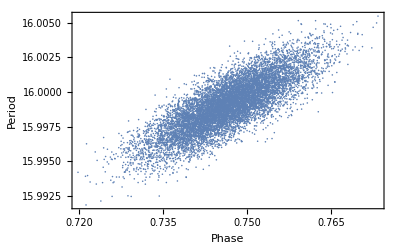

```mathematica
Histogram[xx[[All,1]],Frame->True,Axes->False,FrameLabel->{"Phase","N"}]
Histogram[xx[[All,2]],Frame->True,Axes->False,FrameLabel->{"Period (days)","N"}]
Histogram[Exp[xx[[All,3]]],Frame->True,Axes->False,FrameLabel->{"K (m/s)","N"}]
ListPlot[xx[[All,{1,2}]],Frame->True,Axes->False,FrameLabel->{"Phase","Period"}]
```